(Energy-V) ψ[x,t]+a ψ^(2,0)[x,t]==0

{{ψ→Function[{x,t},(-3^(2/3) AiryAi[2^(2/3) (-1/2+x/2)] AiryBi[-1/2^(1/3)] Gamma[2/3]+3^(2/3) AiryAi[-1/2^(1/3)] AiryBi[2^(2/3) (-1/2+x/2)] Gamma[2/3])/(√3 AiryAi[-1/2^(1/3)]-AiryBi[-1/2^(1/3)])]}}

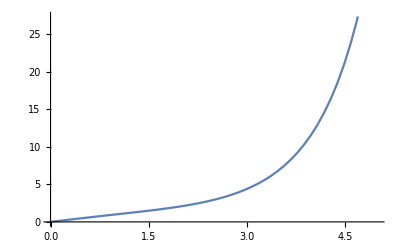

```mathematica
diffEquation[a_, Energy_, V_]=a*D[ψ[x, t], {x, 2}]+(Energy-V)*ψ[x, t]==0
DSolve[{diffEquation[2, 1, x], ψ[0, t]==0, ψ[1, t]==1},ψ,{x, t}]
Plot[ψ[x, 0]/.%, {x, 0, 5}]
```

```mathematica
diffEquation[a_, Energy_, V_]=a*D[ψ[x, t], {x, 2}]+(Energy-V)*ψ[x, t]==0
DSolve[{diffEquation[2, 1, x], ψ[0, t]==0, ψ[1, t]==1},ψ,{x, t}]
Plot[ψ[x, 0]/.%, {x, 0, 5}]
```

(Energy-V) ψ[x,t]+a ψ^(2,0)[x,t]==0

{{ψ→Function[{x,t},(-3^(2/3) AiryAi[2^(2/3) (-1/2+x/2)] AiryBi[-1/2^(1/3)] Gamma[2/3]+3^(2/3) AiryAi[-1/2^(1/3)] AiryBi[2^(2/3) (-1/2+x/2)] Gamma[2/3])/(√3 AiryAi[-1/2^(1/3)]-AiryBi[-1/2^(1/3)])]}}

-Graphics-

```mathematica
equation=a*D[ψ[x, t], {x, 2}]+(Energy-V)*ψ[x, t]==0
nSol=NDSolve[{equation, a==15, Energy==13, V==1},ψ,{x,0,30}]
Plot[Evaluate[ψ[x, 0]/.nSol],{x,0,30},PlotRange->All]
```

(Energy-V) ψ[x,t]+a ψ^(2,0)[x,t]==0

ConstantArray::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of ConstantArray[{TemporaryVariable$166875},-∞].

Take::take: Cannot take positions 1 through 2 in {False}.

{{ψ→ψ}}

-Graphics-